```mathematica
(* https://math.stackexchange.com/questions/171462/fourier-transform-of-function-composition *)
```

```mathematica
(* f[x_]:=HeavisidePi[x]; *)
```

```mathematica
Off[General::munfl]
```

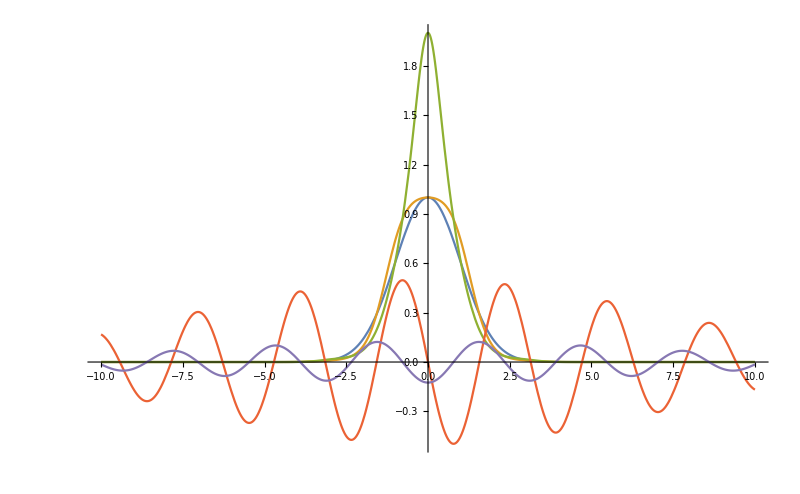

```mathematica
f[x_]:=Exp[-x^2/2];
ψ[x_]:=-1/4*Exp[-0.01*x^2]*Sin[2*x];
Plot[{f[x],f[x+ψ[x]],f[x+ψ[x]]/(1+ψ'[x]),2*ψ[x],0.25*ψ'[x]},{x,-10,10},PlotRange->All,Exclusions->None,ImageSize->{800,600}]
```